# Infinite tree of circles

```mathematica
EightWaySymmetry[pixelList_] := Module[{n = Length[pixelList], i, newPixelList = {}, x, y},
	For[i = 1, i <= n, i++,
		{x, y} = pixelList[[i]];
		AppendTo[newPixelList, {x, y}];
		AppendTo[newPixelList, {y, x}];
		AppendTo[newPixelList, {-y, x}];
		AppendTo[newPixelList, {-x, y}];
		AppendTo[newPixelList, {-x, -y}];
		AppendTo[newPixelList, {-y, -x}];
		AppendTo[newPixelList, {y, -x}];
		AppendTo[newPixelList, {x, -y}];
	];
	Return[newPixelList];
]
```

```mathematica
DrawCircle[origin_, r_]:=Module[{pixelList = {}, h, x, y, dU, dD},
	h = 1 - r;
	x = 0;
	y = r;
	AppendTo[pixelList, {x, y}];
	
	While[y > x,
		If[h < 0, 
			dU = 2 * x + 3;
			h = h + dU;
			,
			dD = 2 * (x - y) + 5;
			h = h + dD;
			y = y - 1;
		];
		x = x + 1;
		AppendTo[pixelList, {x, y}];
	];
	pixelList = EightWaySymmetry[pixelList];
	pixelList = # + origin & /@ pixelList;
	Return[pixelList];
]
```

```mathematica
DrawPixel[pointList_] := Module[{},
	Return[Table[{Blue,Rectangle[pointList[[i]], pointList[[i]] + {1,1}]},{i, Length[pointList]}]];
]
```

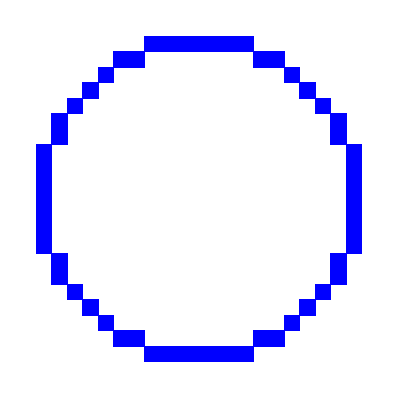

```mathematica
Graphics[DrawPixel[DrawCircle[{10,10}, 10]]]
```

```mathematica
InfiniteCircle[origin_, r_, n_] := Module[{pixelList={}},
	If[n == 0,
		Return[pixelList];
	];
	pixelList = Join[pixelList, DrawPixel[DrawCircle[origin, r]]];
	pixelList = Join[pixelList, InfiniteCircle[{origin[[1]] + r + r/2, origin[[2]]}, r/2, n - 1]];
	pixelList = Join[pixelList, InfiniteCircle[{origin[[1]] - r - r/2, origin[[2]]}, r/2, n - 1]];
	pixelList = Join[pixelList, InfiniteCircle[{origin[[1]] , origin[[2]] - r - r/2}, r/2, n - 1]];
	pixelList = Join[pixelList, InfiniteCircle[{origin[[1]] , origin[[2]] + r + r/2}, r/2, n - 1]];
	Return[pixelList];
]
```

```mathematica
Graphics[InfiniteCircle[{0,0}, 800, 6]]
```

-Graphics-